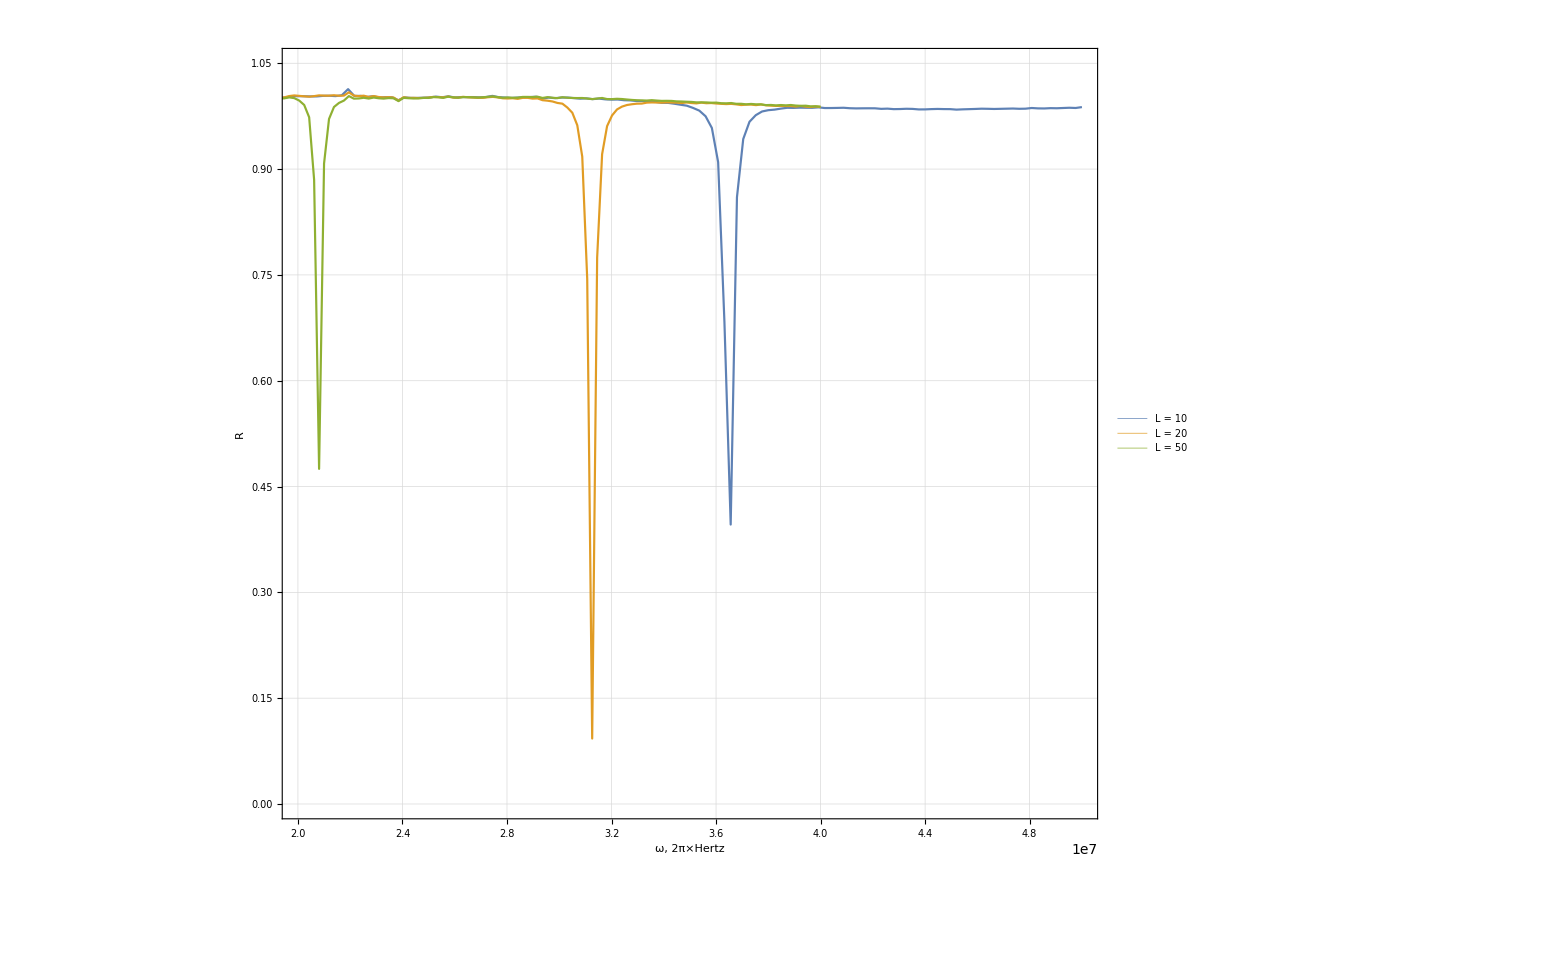

```mathematica
SetDirectory[NotebookDirectory[]];
Import[#][[19;;-2]]&/@{"QQ9.csv", "QQ4.csv","QQ5.csv"};
ListLinePlot[%, 
PlotRange->{{2*10^7,5*10^7},{0, 1.05}},
PlotLegends->Placed[
{{"L = 10", "L = 20", "L = 50"}},
{0.08,0.15}
],
PlotTheme->"Detailed",
PlotStyle->Thickness[0.001],
FrameLabel->{Style["ω, 2π×Hertz", 17], Style["R", 17]},
FrameStyle->Directive[Black, 15],
ImageSize->Large
]
(*Export["../images/R_plot_C_22.png",%, ImageResolution->500]*)
```

```mathematica
height = 0.47631;
omega = 2.08;
left=2.07144;
right=2.08573;
1-(1-height)/√2
omega/Abs[left-right]
```

0.629695

145.556

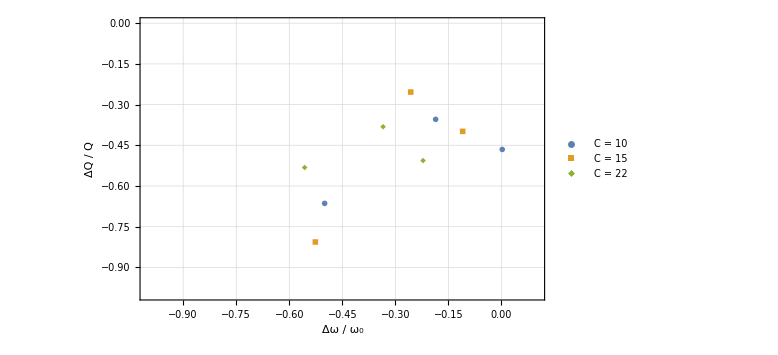

../images/Q_w_plot.png

```mathematica
val10 = {{44.7, 223.5},{36.3, 269.9}, {22.3, 140.4}};
val15 = {{40.6, 216.5}, {33.9, 268.6}, {21.6, 69.7}};
val22 = {{36.5,153.5}, {31.2, 192.3}, {20.8, 145.6}};
center[ w_,Q_]:={(First@#-w)/w, (Last@# - Q)/Q}&
val10 = center[44.6,418]/@val10;
val15 = center[45.6,360]/@val15;
val22 = center[46.9,311]/@val22;

ListPlot[{val10, val15, val22},
PlotRange->{{-1,0.1},{-1, 0}},
PlotLegends->Placed[
{{"C = 10", "C = 15", "C = 22"}},
{0.08,0.15}
],
PlotMarkers->{Automatic, Large},
PlotTheme->"Detailed",
FrameLabel->{Style["Δω / ω_0", 17], Style["ΔQ / Q", 17]},
FrameStyle->Directive[Black, 15],
ImageSize->Large
]
Export["../images/Q_w_plot.png",%, ImageResolution->500]
```